```mathematica
data = Import[NotebookDirectory[] ~~ "pokemon_alopez247.csv"]
```

```mathematica
dataWithoutHeader = data[[2;; Length[data]]]
trainingData = RandomSample[ dataWithoutHeader, Floor[0.8*Length[dataWithoutHeader]]]
testData = Select[dataWithoutHeader, (! MemberQ[trainingData, #])&];
```

```mathematica
XTrain = Transpose[ Transpose[ trainingData][[1;;Length[Transpose[trainingData]]-1]] ];
XTest = Transpose[ Transpose[ testData][[1;;Length[Transpose[testData]]-1 ]]]
```

```mathematica
YTrain = Transpose[  trainingData][[Length[Transpose[trainingData]]]];
YTest = Transpose[  testData][[Length[Transpose[testData]]]];
```

```mathematica
model = Predict[XTrain -> YTrain,Method->"NeuralNetwork"]
```

PredictorFunction[…]

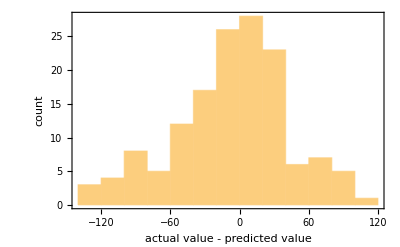

```mathematica
mesurment = PredictorMeasurements[model, XTest -> YTest,"ResidualHistogram"]
```

```mathematica
%//Sqrt
```

45.5677

```mathematica
%/255//N
```

0.178697

```mathematica
model//PredictorInformation
```

Predictor information
Method | Neural network
Number of features | 9
Number of training examples | 576
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1
Number of hidden layers | 2
Hidden nodes | ,,2727
Hidden layer activation functions | ,,TanhTanh
CostFunction | Cost Function